Storage effect with age structure, viability selection during the laval stage

```mathematica
Rep=1; (* number of replicates *)
Cap=5000; (* laval population size *)
senv =0.2; sran=0.1; (* senv = a_S, sran = b_S *)
lenv=0.25; lran=0.05;  (* lenv = a_L, lran = b_L *)

dregul=-1; (* dregul is parameter g in Kim (2023); a large positive value sets soft selection. A negative value sets hard selection *)
Lseq=4; (* the number of loci *)
NSelSite=4;  (* the number of loci under selection; as this study does not include neutral loci, you need to set Lseq = NSelSite *)
selco=Table[{0,1},{l,1,NSelSite}];
selco=Join[selco,Table[{0,0},{l,1,Lseq-NSelSite}]];
rmut=0.00002; (* mutation rate per locus per generation *)
eL=0.7;(* probability for a haploid advancing from the larval to subadult stage *)
eS=0.7;(* probability for a haploid advancing from the subadult to adult stage *)
rrec=0.03; (* recombination rate between adjacent loci per generation *)
TotGen=50000; (* maximum length (generation) of a single simulation run *)
intvl=5000;
cvlist={};
mTfix = {};
mfixed=Table[0,{l,1,NSelSite}];
nfixed=0;

For[rep=0,rep<Rep,rep++;
LFreqTraj={};
SFreqTraj={};
AFreqTraj={};
NPopTraj={};
PLav={Cap};HLav={0}; (* HLav = haplotype list, PLav = corresponding number (>0) of individuals in the larval stage *)
PSub={Cap eL};HSub={0}; (* number and haplotype lists in the subadult stage *)
PAdu={Cap eL eS};HAdu={0}; (* number and haplotype lists in the adult stage *)
mHetTraj={};
gen=0;
fixed=Table[0,{l,1,NSelSite}];
AF=mHet=Table[0,{l,1,Lseq}];
mmHet=0;
m01=m15=m59=m910=0;
fcount=0;
While[
gen<TotGen,
gen++;

{PSub,HSub}=Mutation[PSub, HSub, rmut Lseq, Lseq];
{PSub,HSub}=Recombination[PSub, HSub, rrec( Lseq-1), Lseq];
{PAdu,HAdu}=Mutation[PAdu, HAdu, rmut Lseq, Lseq];
{PAdu,HAdu}=Recombination[PAdu, HAdu, rrec( Lseq-1), Lseq];

{Parent,HParent}=MergePops[PSub, HSub, PAdu, HAdu];(* merging subadults and adults before reproduction *)
env=RandomVariate[NormalDistribution[]]; (* sampling the environment (Z1) *)
HFitL=HaploFit[HParent, AMFfitRF[env,senv, sran, selco,Lseq],Lseq];
KLaval=Cap Exp[lenv env+lran RandomVariate[NormalDistribution[]]]; (* sampling the carrying capacity of the larval stage *)
{POffs,HOffs}=PoissonReproduceRF[Parent, HParent,HFitL, KLaval, dregul];

NL=Total[POffs];nHL=Length[POffs];
NP=Total[Parent];
If[(NL==0)||(NP==0),Print["Extinct ",{gen,NL,NP}];Break[]];

{PAdu,HAdu}=Advance[PSub,HSub,eS];
{PSub,HSub}=Advance[PLav,HLav,eL];
{PLav,HLav}={POffs,HOffs};
NS=Total[PSub];nHS=Length[PSub];
NA=Total[PAdu];nHA=Length[PAdu];

LFreq=Table[Count1[PLav, HLav,nHL,st],{st,1,Lseq}]; (* counting mutant frequencies at all loci in the larval stage *)
LFreqTraj=Append[LFreqTraj,LFreq];
SFreq=Table[Count1[PSub, HSub,nHS,st],{st,1,Lseq}];
SFreqTraj=Append[SFreqTraj,SFreq];
AFreq=Table[Count1[PAdu, HAdu,nHA,st],{st,1,Lseq}];
AFreqTraj=Append[AFreqTraj,AFreq];
NPopTraj=Append[NPopTraj,{NL,NS,NA}];

For[site=0,site<Lseq,site++;
AF[[site]]=1.0(LFreq[[site]]+SFreq[[site]]+AFreq[[site]])/(NL+NS+NA);
mHet[[site]]+=2AF[[site]](1-AF[[site]]); (* site heterozygosity *)
If[AF[[site]]<0.1, m01++,
If[AF[[site]]<0.5,m15++,If[AF[[site]]<0.9,m59++, m910++]] ];
If[fixed[[site]]==0,
If[AF[[site]]>0.9, fixed[[site]]=gen; fcount++] 
]
];

If[Mod[gen,intvl]==0,
Print[gen, AF,{NL, NS, NA}]
]
];

For[site=0, site<Lseq,site++;
mHet[[site]]/=gen;
mmHet +=mHet[[site]]/Lseq;
];
Print[mHet," het=",mmHet];
m01/=(Lseq gen);m15/=(Lseq gen); m59/=(Lseq gen);m910/=(Lseq gen);
Print["p[0,0.1]=",1.0 m01," p[0.1,0.5]=", 1.0 m15," p[0.5,0.9]=",1.0m59, " p[0.9,1]=",1.0m910];

If[
fcount==NSelSite,
mTfix=Append[mTfix,Mean[fixed]]; (* recording the fixation times averaged over loci *)
fixed=Sort[fixed];
mfixed=mfixed+fixed;
nfixed++;
If[Lseq>1,
cv =1.0 StandardDeviation[fixed]/Mean[fixed]; (* coefficient of variation for fixation times *)
cvlist=Append[cvlist, cv],
cv=0
];
Print[rep,fixed," cv= ", cv];
];
];
TAllFix=gen;

Print[cvlist];
Print[" mTfix = ", 1.0 Mean[mTfix]]; (* mean fixation time across replicates *)
If[Lseq>1,Print[ "mean cv = ", Mean[cvlist]]]
```

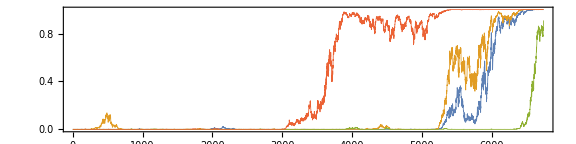

```mathematica
RelFreqList=Table[(LFreqTraj[[gen]][[site]]+SFreqTraj[[gen]][[site]]+AFreqTraj[[gen]][[site]])/Total[NPopTraj[[gen]]],{site,1,Lseq},{gen,1,TAllFix}];
gFreq=ListPlot[RelFreqList,Joined->True,Frame->True, PlotStyle->Thickness[0.001],PlotRange->{0,1},AspectRatio->0.25, ImageSize->Large](* plotting the A2 allele frequencies at all loci *)
```

```mathematica
Export["C:\\Users\\이화여자대학교\\Dropbox\\Research\\AbsFluc\\AgeStruc\\gFly1006e.tif",gFreq,"TIFF"]
```

C:\Users\이화여자대학교\Dropbox\Research\AbsFluc\AgeStruc\gFly1006e.tif

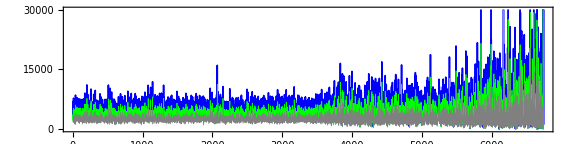

```mathematica
NLList=Table[NPopTraj[[gen, 1]],{gen,1,TAllFix}];
NSList=Table[NPopTraj[[gen, 2]],{gen,1,TAllFix}];
NAList=Table[NPopTraj[[gen, 3]],{gen,1,TAllFix}];
gNpop=ListPlot[{NLList, NSList, NAList},Joined->True,Frame->True, PlotStyle->{{Thickness[0.002],Blue},{Thickness[0.001],Green},{Thickness[0.0005],Gray}},PlotRange->{0,30000},AspectRatio->0.25, ImageSize->Large] (* plotting total population size over time *)
```